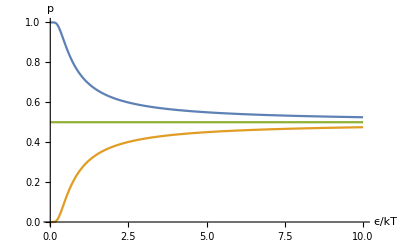

```mathematica
Plot[{1/(1+Exp[-1/x]),1/(1+Exp[1/x]),1/2},{x,0,10},PlotRange->Full,AxesLabel->{"ϵ/kT","p"},LabelStyle->Medium]
```

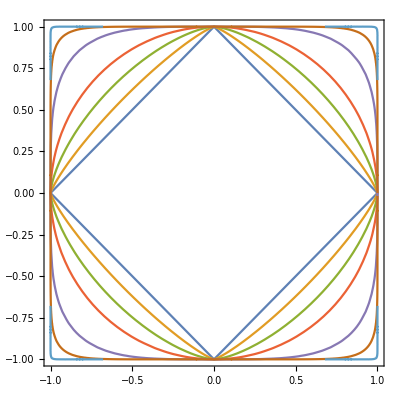

```mathematica
ContourPlot[{1==Abs[x]+Abs[y],1==Abs[x]^1.2+Abs[y]^1.2,1==Abs[x]^1.5+Abs[y]^1.5,1==Abs[x]^2+Abs[y]^2,1==Abs[x]^4+Abs[y]^4,1==Abs[x]^10+Abs[y]^10,1==Abs[x]^100+Abs[y]^100},{x,-1,1},{y,-1,1}]
```

```mathematica
Table[1==Abs[x]^s+Abs[y]^s,{s,{1,1.2,1.5,2,4,10}}]
```

{1==Abs[x]+Abs[y],1==Abs[x]^1.2+Abs[y]^1.2,1==Abs[x]^1.5+Abs[y]^1.5,1==Abs[x]^2+Abs[y]^2,1==Abs[x]^4+Abs[y]^4,1==Abs[x]^10+Abs[y]^10}

```mathematica
Integrate[(1-Cos[kx 4 + ky 5])/(kx^2+ky^2),{kx,-Pi,Pi},Assumptions->{ky ∈ Reals}]
```

ConditionalExpression[1/(2 ky)(4 ArcTan[π/ky]-2 ⅈ Cos[5 ky] Cosh[4 ky] CosIntegral[-4 ⅈ ky]+2 ⅈ Cos[5 ky] Cosh[4 ky] CosIntegral[4 ⅈ ky]+ⅈ Cos[(5+4 ⅈ) ky] CosIntegral[-4 ⅈ ky+4 π]+ⅈ Cosh[(4+5 ⅈ) ky] CosIntegral[-4 ⅈ ky+4 π]-ⅈ Cos[(5+4 ⅈ) ky] CosIntegral[4 ⅈ ky+4 π]-ⅈ Cosh[(4+5 ⅈ) ky] CosIntegral[4 ⅈ ky+4 π]+ⅈ Sin[(5+4 ⅈ) ky] SinIntegral[4 ⅈ ky-4 π]-Sinh[(4+5 ⅈ) ky] SinIntegral[4 ⅈ ky-4 π]-ⅈ Sin[(5+4 ⅈ) ky] SinIntegral[4 ⅈ ky+4 π]+Sinh[(4+5 ⅈ) ky] SinIntegral[4 ⅈ ky+4 π]),ky≠0]

```mathematica
Integrate[1/(2 ky)(4 ArcTan[π/ky]-2 ⅈ Cos[5 ky] Cosh[4 ky] CosIntegral[-4 ⅈ ky]+2 ⅈ Cos[5 ky] Cosh[4 ky] CosIntegral[4 ⅈ ky]+ⅈ Cos[(5+4 ⅈ) ky] CosIntegral[-4 ⅈ ky+4 π]+ⅈ Cosh[(4+5 ⅈ) ky] CosIntegral[-4 ⅈ ky+4 π]-ⅈ Cos[(5+4 ⅈ) ky] CosIntegral[4 ⅈ ky+4 π]-ⅈ Cosh[(4+5 ⅈ) ky] CosIntegral[4 ⅈ ky+4 π]+ⅈ Sin[(5+4 ⅈ) ky] SinIntegral[4 ⅈ ky-4 π]-Sinh[(4+5 ⅈ) ky] SinIntegral[4 ⅈ ky-4 π]-ⅈ Sin[(5+4 ⅈ) ky] SinIntegral[4 ⅈ ky+4 π]+Sinh[(4+5 ⅈ) ky] SinIntegral[4 ⅈ ky+4 π]),{ky,-Pi,Pi}]
```

```mathematica
Integrate[Cos[x Cos[phi]],{phi,0,2Pi}]
```

ConditionalExpression[2 π BesselJ[0,Abs[x]],x∈Reals]

```mathematica
Integrate[(1-BesselJ[0,k*x])/k,{k,0,Pi}]
```

ConditionalExpression[1/8 π^2 x^2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 π^2 x^2],Re[x]≥0&&Im[x]==0]

```mathematica
Series[1/8 π^2 x^-2 HypergeometricPFQ[{1,1},{2,2,2},-1/4 π^2 x^-2],{x,0,0}]
```

```mathematica
Assuming[Arg[x]==0, Refine[ⅇ^(-7/2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]) ((-1)^Floor[(π+2 Arg[x])/(2 π)] ⅇ^((-1)^Floor[(π+2 Arg[x])/(2 π)] (-(ⅈ π)/x+O[x]^2)) O[x]^2+(-1)^Floor[(π+2 Arg[x])/(2 π)] ⅇ^((-1)^Floor[(π+2 Arg[x])/(2 π)] ((ⅈ π)/x+O[x]^2)) O[x]^2+ⅇ^((-1)^Floor[(π+2 Arg[x])/(2 π)] ((ⅈ π)/x+O[x]^2)) (((-1)^(1/4) x^(3/2))/(√2 π^2)+O[x]^2)+ⅇ^((-1)^Floor[(π+2 Arg[x])/(2 π)] (-(ⅈ π)/x+O[x]^2)) (-((-1)^(3/4) x^(3/2))/(√2 π^2)+O[x]^2)+ⅇ^(7/2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]) (1/2 (2 EulerGamma+Log[π^2/4]-2 Log[x])+O[x]^1))]]
```

ⅇ^(-(ⅈ π)/x+O[x]^2) O[x]^2+ⅇ^((ⅈ π)/x+O[x]^2) O[x]^2+ⅇ^((ⅈ π)/x+O[x]^2) (((-1)^(1/4) x^(3/2))/(√2 π^2)+O[x]^2)+ⅇ^(-(ⅈ π)/x+O[x]^2) (-((-1)^(3/4) x^(3/2))/(√2 π^2)+O[x]^2)+(1/2 (2 EulerGamma+Log[π^2/4]-2 Log[x])+O[x]^1)

```mathematica
((-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
   E^((-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
     SeriesData[x, 0, {(-I)*Pi}, -1, 2, 1])*
   SeriesData[x, 0, {}, 4, 4, 2] + 
  (-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
   E^((-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
     SeriesData[x, 0, {I*Pi}, -1, 2, 1])*
   SeriesData[x, 0, {}, 4, 4, 2] + 
  E^((-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
     SeriesData[x, 0, {I*Pi}, -1, 2, 1])*
   SeriesData[x, 0, {(-1)^(1/4)/(Sqrt[2]*Pi^2)}, 3, 
    4, 2] + E^((-1)^Floor[(Pi + 2*Arg[x])/(2*Pi)]*
     SeriesData[x, 0, {(-I)*Pi}, -1, 2, 1])*
   SeriesData[x, 0, {-((-1)^(3/4)/(Sqrt[2]*Pi^2))}, 
    3, 4, 2] + 
  E^(((7*I)/2)*Pi*Floor[(Pi + 2*Arg[x])/(2*Pi)])*
   SeriesData[x, 0, {(2*EulerGamma + Log[Pi^2/4] - 
       2*Log[x])/2}, 0, 1, 1])/
 E^(((7*I)/2)*Pi*Floor[(Pi + 2*Arg[x])/(2*Pi)])
```

```mathematica
Integrate[1/x^4 (G Exp[-k s x] / x + 1),{x,1,Infinity}]
```

ConditionalExpression[1/3-1/48 ⅇ^(-k s) G (-12+4 k s-2 k^2 s^2+2 k^3 s^3+2 ⅇ^(k s) k^4 s^4 ExpIntegralEi[-k s]+ⅇ^(k s) k^4 s^4 Log[-1/(k s)]-ⅇ^(k s) k^4 s^4 Log[-k s]+2 ⅇ^(k s) k^4 s^4 Log[k s]),Re[k s]>0]

```mathematica
f = 1 + Q1 x + Q2 x^2 + Q3 x^3 + Q4 x^4
```

1+Q1 x+Q2 x^2+Q3 x^3+Q4 x^4

```mathematica
Series[Log[f],{x,0,4}]
```

Q1 x+(-Q1^2/2+Q2) x^2+(Q1^3/3-Q1 Q2+Q3) x^3+(-Q1^4/4+Q1^2 Q2-Q2^2/2-Q1 Q3+Q4) x^4+O[x]^5

```mathematica
Series[x(1-BesselJ[0,1/x]),{x,0,1},Assumptions->{x∈Reals,x>0}]
```

(x+O[x]^2)+Cos[π/4-1/x] (-√(2/π) x^(3/2)+O[x]^(5/2))+(x^(5/2)/(4 √(2 π))+O[x]^3) Sin[π/4-1/x]

```mathematica
BesselJ[0,0]
```

1

```mathematica
D[BesselJ[0,x],x]
```

-BesselJ[1,x]

```mathematica
Series[BesselJ[0,x],{x,0,10}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+O[x]^11

```mathematica
f = 1 + Q1 x + Q2 x^2 + Q3 x^3 + Q4 x^4
```

1+Q1 x+Q2 x^2+Q3 x^3+Q4 x^4

```mathematica
ff = 1 + Q1 x + 1/2Q2 x^2 + 1/6Q3 x^3 + 1/24Q4 x^4
```

1+Q1 x+(Q2 x^2)/2+(Q3 x^3)/6+(Q4 x^4)/24

```mathematica
Series[Log[ff],{x,0,4}]
```

Q1 x+1/2 (-Q1^2+Q2) x^2+1/6 (2 Q1^3-3 Q1 Q2+Q3) x^3+1/24 (-6 Q1^4+12 Q1^2 Q2-3 Q2^2-4 Q1 Q3+Q4) x^4+O[x]^5

```mathematica
Solve[16c^5 - 20c^3 + 5c + 1 == 0,c]
```

{{c→-1},{c→1/4 (1-√5)},{c→1/4 (1-√5)},{c→1/4 (1+√5)},{c→1/4 (1+√5)}}

```mathematica
(c-(1-Sqrt[5])/4)*(c-(1+Sqrt[5])/4)
```

(1/4 (-1-√5)+c) (1/4 (-1+√5)+c)

```mathematica
Expand[%]
```

-1/4-c/2+c^2

```mathematica
M = {{Cos[p]-1,Cos[p]-Cos[2p]},{Sin[p],Sin[p]-Sin[2p]}};
V = {Cos[p/2]+Cos[p],Sin[p]};
Solve[M.{an1,an2}==V,{an1,an2}]
```

{{an1→-(-Cos[p/2] Sin[p]-Cos[2 p] Sin[p]+Cos[p/2] Sin[2 p]+Cos[p] Sin[2 p])/(-Sin[p]+Cos[2 p] Sin[p]+Sin[2 p]-Cos[p] Sin[2 p]),an2→-((1+Cos[p/2]) Sin[p])/(-Sin[p]+Cos[2 p] Sin[p]+Sin[2 p]-Cos[p] Sin[2 p])}}

```mathematica
FullSimplify[%]
```

{{an1→1/8 (-8 Cos[p/2]+Csc[p/4]^2),an2→1/8 Csc[p/4]^2}}

```mathematica
%/.p->2Pi/5
```

{{an1→1/8 (-2 (1+√5)+(1+√5)^2),an2→1/8 (1+√5)^2}}

```mathematica
N[%]
```

{{an1→0.5,an2→1.30902}}

```mathematica
TrigExpand[%]
```

{{t1→3/4 Cot[p/2]+1/4 Csc[p/2]^2-1/2 Csc[p/2] Sec[p/2]-1/4 Tan[p/2],t2→1/4 Csc[p/2]^2+1/4 Csc[p/2] Sec[p/2]}}

```mathematica
FullSimplify[%]
```

{{t1→1/4 (Cot[p/2]+Csc[p/2]^2-3 Tan[p/2]),t2→1/4 (Csc[p/2]^2+2 Csc[p])}}

```mathematica
%%
```

{{t1→1/4 (Cot[p/2]+Csc[p/2]^2-3 Tan[p/2]),t2→1/4 (Csc[p/2]^2+2 Csc[p])}}

```mathematica
%/. p->2Pi/5
```

{{t1→1/4 (√(1+2/(√5))-3 √(5-2 √5)+1/(5/8-(√5)/8)),t2→(1+√(5-2 √5))/(2+1/2 (1-√5))}}

```mathematica
FullSimplify[%]
```

{{t1→1/2 (1+1/(√5)-√(10-22/(√5))),t2→1/10 (5+√5+√(50-10 √5))}}

```mathematica
N[%]
```

{{t1→0.522795,t2→1.24934}}

```mathematica
t[p_] := 1/4 (Cot[p/2]+Csc[p/2]^2-3 Tan[p/2])
```

```mathematica
t[2Pi/5.]
```

0.522795

```mathematica
1/4((1+Cos[p])^2/Sin[p])^2 * (Sin[p]/(1+Cos[p]) + Sin[p]^2/(1+Cos[p])^2 + 1 - 3 Sin[p]^3/(1+Cos[p])^3)
```

1/4 (1+Cos[p])^4 Csc[p]^2 (1+Sin[p]/(1+Cos[p])+Sin[p]^2/(1+Cos[p])^2-(3 Sin[p]^3)/(1+Cos[p])^3)

```mathematica
TrigExpand[%]
```

-7/8-(3 Cos[p])/4-(3 Cos[p]^2)/16+15/(128 (1+Cos[p])^2)+(15 Cos[p])/(16 (1+Cos[p])^2)+(39 Cos[p]^2)/(32 (1+Cos[p])^2)+(5 Cos[p]^3)/(8 (1+Cos[p])^2)+(15 Cos[p]^4)/(128 (1+Cos[p])^2)-(33 Cot[p])/(16 (1+Cos[p])^3)-(99 Cos[p] Cot[p])/(256 (1+Cos[p])^3)+(3 Cos[p]^2 Cot[p])/(2 (1+Cos[p])^3)+(375 Cos[p]^3 Cot[p])/(256 (1+Cos[p])^3)+(9 Cos[p]^4 Cot[p])/(16 (1+Cos[p])^3)+(21 Cos[p]^5 Cot[p])/(256 (1+Cos[p])^3)+(3 Cot[p])/(2 (1+Cos[p]))+(81 Cos[p] Cot[p])/(64 (1+Cos[p]))+(Cos[p]^2 Cot[p])/(2 (1+Cos[p]))+(5 Cos[p]^3 Cot[p])/(64 (1+Cos[p]))+(7 Cot[p]^2)/8+1/4 Cos[p] Cot[p]^2+1/32 Cos[p]^2 Cot[p]^2-(15 Cot[p]^2)/(128 (1+Cos[p])^2)-(5 Cos[p] Cot[p]^2)/(16 (1+Cos[p])^2)-(13 Cos[p]^2 Cot[p]^2)/(64 (1+Cos[p])^2)-(Cos[p]^3 Cot[p]^2)/(16 (1+Cos[p])^2)-(Cos[p]^4 Cot[p]^2)/(128 (1+Cos[p])^2)-(297 Csc[p])/(256 (1+Cos[p])^3)+(21 Csc[p])/(32 (1+Cos[p]))+7/4 Cot[p] Csc[p]+(3 Cot[p] Csc[p])/(8 (1+Cos[p])^2)+(35 Csc[p]^2)/32+(21 Csc[p]^2)/(64 (1+Cos[p])^2)+(33 Sin[p])/(256 (1+Cos[p])^3)-(3 Cos[p] Sin[p])/(2 (1+Cos[p])^3)-(375 Cos[p]^2 Sin[p])/(128 (1+Cos[p])^3)-(15 Cos[p]^3 Sin[p])/(8 (1+Cos[p])^3)-(105 Cos[p]^4 Sin[p])/(256 (1+Cos[p])^3)-(27 Sin[p])/(64 (1+Cos[p]))-(Cos[p] Sin[p])/(2 (1+Cos[p]))-(5 Cos[p]^2 Sin[p])/(32 (1+Cos[p]))+Sin[p]^2/32-(13 Sin[p]^2)/(64 (1+Cos[p])^2)-(5 Cos[p] Sin[p]^2)/(16 (1+Cos[p])^2)-(15 Cos[p]^2 Sin[p]^2)/(128 (1+Cos[p])^2)+(75 Sin[p]^3)/(256 (1+Cos[p])^3)+(9 Cos[p] Sin[p]^3)/(16 (1+Cos[p])^3)+(63 Cos[p]^2 Sin[p]^3)/(256 (1+Cos[p])^3)+Sin[p]^3/(64 (1+Cos[p]))+Sin[p]^4/(128 (1+Cos[p])^2)-(3 Sin[p]^5)/(256 (1+Cos[p])^3)

```mathematica
FullSimplify[%]
```

(3+4 Cos[p]+Cos[2 p]-Sin[p]+Sin[2 p]+Sin[3 p])/(4-4 Cos[p])

```mathematica
FullSimplify[1-%]
```

(-1+8 Cos[p]+Cos[2 p]-Sin[p]+Sin[2 p]+Sin[3 p])/(4 (-1+Cos[p]))

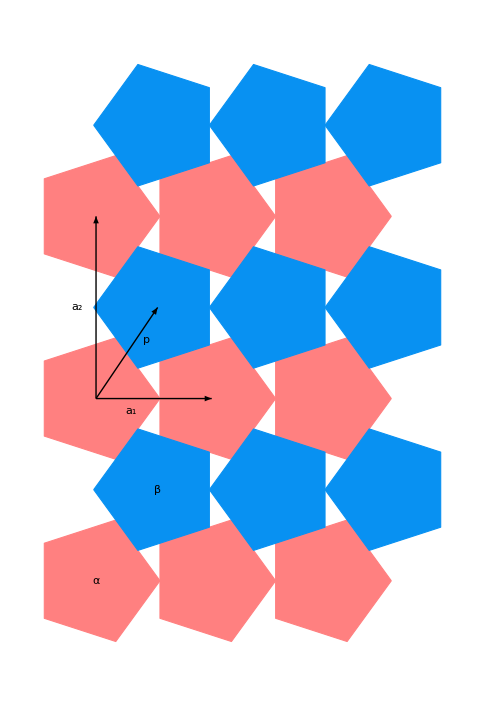

```mathematica
t1 = 1/4 (Cot[Pi/5]+Csc[Pi/5]^2-3 Tan[Pi/5]);
t1=1/2;
d1 = 1+Cos[Pi/5];
d2 = 2(1+t1)Sin[2Pi/5];
px = (1-t1+Cos[2Pi/5]+t1 Cos[2Pi/5]);
py = (1+t1)Sin[2Pi/5];
Centers1 = Flatten[Table[{n1*d1,n2*d2},{n1,0,2},{n2,0,2}],1];
Centers2 = Table[Centers1[[i]] + {px,py},{i,1,Length[Centers1]}];
R = {{Cos[2Pi/5],-Sin[2Pi/5]},{Sin[2Pi/5],Cos[2Pi/5]}};
Vertices1= Table[Table[Centers1[[i]]+MatrixPower[R,n].{1,0},{n,0,4}],{i,1,Length[Centers1]}];
Vertices2 = Table[Table[Centers2[[i]]+MatrixPower[R,n].{-1,0},{n,0,4}],{i,1,Length[Centers2]}];

P1=Table[Graphics[{EdgeForm[Thick],Pink,Polygon[Vertices1[[i]]]}],{i,1,Length[Vertices1]}];
P2=Table[Graphics[{EdgeForm[Thick],RGBColor[0.03,0.57,0.95],Polygon[Vertices2[[i]]]}],{i,1,Length[Vertices2]}];
a1 = Graphics[{Thick,Arrow[{{0,d2},{d1,d2}}]}];
a2label = Graphics[Text[Style["a_2",Large],{-0.3,1.5d2}]];
a1label = Graphics[Text[Style["a_1",Large],{0.3d1,d2-0.2}]];
a2 = Graphics[{Thick,Arrow[{{0,d2},{0,2d2}}]}];
p = Graphics[{Thick,Arrow[{{0,d2},{px,py+d2}}]}];
plabel = Graphics[Text[Style["p",Large],{0.5px+0.3,0.5py+0.2+d2}]];
alphalabel = Graphics[Text[Style["α",Large],{0,0}]];
betalabel = Graphics[Text[Style["β",Large],{px,py}]];
Show[P1,P2,a1,a2,a1label,a2label,p,plabel,alphalabel,betalabel]
```

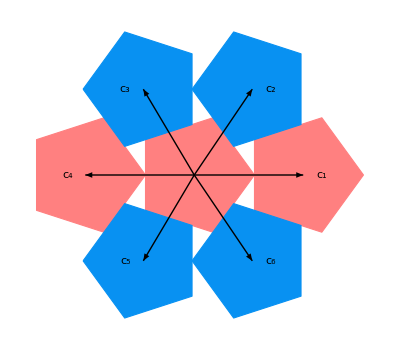

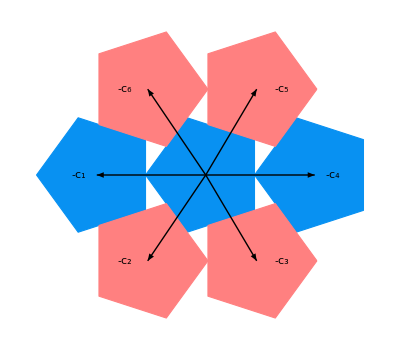

```mathematica
(*alpha centered particle figure*)
P3 = {P1[[{2,5,8}]],P2[[{1,2,4,5}]]};
c = {Graphics[{Thick,Arrow[{{d1,d2},{2d1,d2}}]}],Graphics[{Thick,Arrow[{{d1,d2},{d1+px,d2+py}}]}],Graphics[{Thick,Arrow[{{d1,d2},{px,d2+py}}]}],Graphics[{Thick,Arrow[{{d1,d2},{0,d2}}]}],Graphics[{Thick,Arrow[{{d1,d2},{px,d2-py}}]}],Graphics[{Thick,Arrow[{{d1,d2},{d1+px,d2-py}}]}]};
clabel = {Graphics[Text[Style["c_1",Large],{2d1+0.3,d2}]],Graphics[Text[Style["c_2",Large],{d1+px+0.3,d2+py}]],Graphics[Text[Style["c_4",Large],{-0.3,d2}]],Graphics[Text[Style["c_3",Large],{px-0.3,py+d2}]],Graphics[Text[Style["c_5",Large],{px-0.3,py}]],Graphics[Text[Style["c_6",Large],{px+0.3+d1,py}]]};
Show[P3,c,clabel]
P4 = {P2[[{2,5,8}]],P1[[{5,6,8,9}]]};
c2 = {Graphics[{Thick,Arrow[{{d1+px,d2+py},{2d1+px,d2+py}}]}],Graphics[{Thick,Arrow[{{d1+px,d2+py},{2d1,d2}}]}],Graphics[{Thick,Arrow[{{d1+px,d2+py},{2d1,2d2}}]}],Graphics[{Thick,Arrow[{{d1+px,d2+py},{d1,d2}}]}],Graphics[{Thick,Arrow[{{d1+px,d2+py},{d1,2d2}}]}],Graphics[{Thick,Arrow[{{d1+px,d2+py},{px,d2+py}}]}]};
clabel2 = {Graphics[Text[Style["-c_4",Large],{2d1+0.3,d2}+{px,py}]],Graphics[Text[Style["-c_5",Large],{d1+px+0.3,d2+py}+{px,py}]],Graphics[Text[Style["-c_1",Large],{-0.3,d2}+{px,py}]],Graphics[Text[Style["-c_6",Large],{px-0.5,py+d2}+{px,py}]],Graphics[Text[Style["-c_2",Large],{px-0.5,py}+{px,py}]],Graphics[Text[Style["-c_3",Large],{px+0.3+d1,py}+{px,py}]]};
Show[P4,c2,clabel2]
```

```mathematica
Centers2//N
```

{{0.947774,1.44826},{0.947774,4.34479},{0.947774,7.24132},{2.67432,1.44826},{2.67432,4.34479},{2.67432,7.24132},{4.40086,1.44826},{4.40086,4.34479},{4.40086,7.24132}}

```mathematica
ArcTan[Centers2[[1,2]]/Centers2[[1,1]]]*180./Pi
```

56.7984

```mathematica
ArcTan[Centers2[[1,2]]/(Centers2[[1,1]]-1-Tan[Pi/5])]*180./Pi
```

-61.732

```mathematica
180-61.732-56.7984
```

61.4696

```mathematica
Cos[Pi/5]
```

1/4 (1+√5)

```mathematica
Sin[2Pi/5]
```

√(5/8+(√5)/8)

```mathematica
t1
```

1/4 (√(1+2/(√5))-3 √(5-2 √5)+1/(5/8-(√5)/8))

```mathematica
FullSimplify[%]
```

1/2 (1+1/(√5)-√(10-22/(√5)))

```mathematica
1+%
```

1+1/2 (1+1/(√5)-√(10-22/(√5)))

```mathematica
%*Sin[2Pi/5]*(1+Tan[Pi/5])
```

√(5/8+(√5)/8) (1+√(5-2 √5)) (1+1/2 (1+1/(√5)-√(10-22/(√5))))

```mathematica
FullSimplify[%]
```

1+√(1/10 (65-19 √5))

```mathematica
N[%]
```

2.50049

```mathematica
Asquare =FullSimplify[(1+t1)*Sin[2Pi/5](1+Tan[Pi/5])]
```

1+√(1/10 (65-19 √5))

```mathematica
Apent = Sin[2Pi/5]*5/4
```

5/4 √(5/8+(√5)/8)

```mathematica
Apent/Asquare
```

(5 √(5/8+(√5)/8))/(4 (1+√(1/10 (65-19 √5))))

```mathematica
FullSimplify[%]
```

-5/976 (-115-73 √5+2 √(5 (865+382 √5)))

```mathematica
N[%]
```

0.475435

```mathematica
%*2
```

0.95087

```mathematica
N[d2*d1]
```

5.00098

```mathematica
N[5*Sin[2Pi/5]]
```

4.75528

```mathematica
5 Sin[2Pi/5]/(d2*d1)
```

5/(2 (1+√(5-2 √5)) (1+1/4 (√(1+2/(√5))-3 √(5-2 √5)+1/(5/8-(√5)/8))))

```mathematica
FullSimplify[%]
```

25/(2 (-10+8 √5+√(50-10 √5)))

```mathematica
N[%]
```

0.95087

```mathematica
t1//N
```

0.522795

```mathematica
d1//N
```

1.72654

```mathematica
Sqrt[px^2+py^2]//N
```

1.73082

```mathematica
Sqrt[(px-d1)^2+py^2]//N
```

1.64437

```mathematica
Apent
```

5/4 √(5/8+(√5)/8)

```mathematica
N[Apent]
```

1.18882

```mathematica
N[Asquare]
```

2.50049

```mathematica
5/4*Sin[2Pi/5.]
```

1.18882

```mathematica
2Sin[Pi/5.]*0.5
```

0.587785

```mathematica
d1*d2
```

2 √(5/8+(√5)/8) (1+√(5-2 √5)) (1+1/4 (√(1+2/(√5))-3 √(5-2 √5)+1/(5/8-(√5)/8)))

```mathematica
N[d1*d2]
```

5.00098

```mathematica
d1
```

1+√(5-2 √5)

```mathematica
d2
```

2 √(5/8+(√5)/8) (1+1/4 (√(1+2/(√5))-3 √(5-2 √5)+1/(5/8-(√5)/8)))

```mathematica
N[5*Sin[2Pi/5]/(d1*d2),10]
```

0.9508700694

```mathematica
d1
```

1+√(5-2 √5)

```mathematica
d1
```

1+√(5-2 √5)

```mathematica
d1//N
```

1.72654

```mathematica
N[{d1/2,t1,d2/2,px/2,py/2},10]
```

{0.863271264,0.5227953819,1.448264471,0.473887135,0.7241322355}

```mathematica
N[Cos[2Pi/5],100]
```

0.3090169943749474241022934171828190588601545899028814310677243113526302314094512248536036020946955687

```mathematica
N[1/2*(1+Cos[Pi/5]),20]
```

0.90450849718747371205

```mathematica
d1
```

1+1/4 (1+√5)

```mathematica
d1//N
```

1.80902

```mathematica
Sqrt[px^2+py^2]//N
```

1.72149

```mathematica
Sqrt[(px-d1)^2+py^2]//N
```

1.65831

```mathematica
ArcTan[py/px]*180./Pi
```

55.9646

```mathematica
ArcTan[py/(d1-px)]*180./Pi
```

59.3461

```mathematica
180-%-%%
```

64.6892

```mathematica
d1/2//N
```

0.904508

```mathematica
d2/2//N
```

1.42658

```mathematica
px/2//N
```

0.481763

```mathematica
py/2//N
```

0.713292

```mathematica
P = Sqrt[px^2+py^2];
ArcCos[{-d1+px,py}.{-d1,0}/(Sqrt[{-d1+px,py}.{-d1+px,py}] d1)]*180./Pi
```

59.3461